# 2 Layer System

## Series Expansion

## System Setup

```mathematica
$Assumptions=_Symbol∈Reals;
```

```mathematica
sol = Solve[SubPlus[a] +SubMinus[a]==SubPlus[b]+SubMinus[b] && 
(1-(ξ+ⅈ ζ)/α)SubPlus[a]-(1+(ξ+ⅈ ζ)/α)SubMinus[a]==β/α SubPlus[b]-β/α SubMinus[b] &&
SubPlus[c]== ⅇ^((2 π ⅈ β d)/λ)SubPlus[b] &&
SubMinus[c]== ⅇ^(-(2 π ⅈ β d)/λ)SubMinus[b] &&
SubPlus[c] +SubMinus[c]==SubPlus[d] &&
(1-(ξ+ⅈ ζ)/β)SubPlus[c]-(1+(ξ+ⅈ ζ)/β)SubMinus[c]==γ/β SubPlus[d] &&
SubPlus[a]==1,{SubPlus[a],SubMinus[a],SubPlus[b], SubMinus[b], SubPlus[c], SubMinus[c],SubPlus[d]}];
```

## Reflectance

```mathematica
r[λ_]=sol[[1, 2, 2]] ;
```

```mathematica
Subscript[r, s][x_] = Series[r[λ]/. d/λ-> x, {x, 0,3}] // Normal;
```

```mathematica
Subscript[R, s][x_] = Norm[Subscript[r, s][x]];
```

```mathematica
Subscript[R, N][λ_] = Subscript[R, s][x] /. x -> d/λ // Simplify
```

Norm[(α-γ-2 ⅈ ζ-2 ξ)/(α+γ+2 ⅈ ζ+2 ξ)+(4 ⅈ d π α (β^2-(γ+ⅈ ζ+ξ)^2))/(λ (α+γ+2 ⅈ ζ+2 ξ)^2)+(8 d^2 π^2 α (β^2+(α+ⅈ ζ+ξ) (γ+ⅈ ζ+ξ)) (-β^2+(γ+ⅈ ζ+ξ)^2))/(λ^2 (α+γ+2 ⅈ ζ+2 ξ)^3)-(16 ⅈ d^3 π^3 α (β^2-(γ+ⅈ ζ+ξ)^2) (3 β^4-3 (ζ-ⅈ ξ)^2 (γ+ⅈ ζ+ξ)^2+β^2 (-γ^2-2 (ζ-ⅈ ξ)^2+2 γ (ⅈ ζ+ξ))+α^2 (-β^2+3 (γ+ⅈ ζ+ξ)^2)+2 α (3 (ⅈ ζ+ξ) (γ+ⅈ ζ+ξ)^2+β^2 (2 γ+ⅈ ζ+ξ))))/(3 λ^3 (α+γ+2 ⅈ ζ+2 ξ)^4)]

## Plotting (constant ξ)

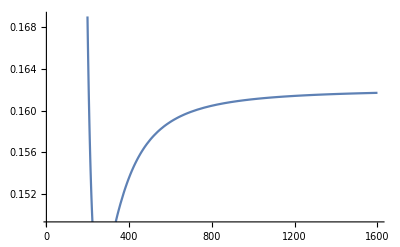

```mathematica
Plot[Subscript[R, N][λ] /. {d-> 20, α-> 1.8, β-> 1.6, γ-> 1.0, ξ-> 0.149, ζ-> 0}, {λ, 20, 1600}]
```

## Graphene Conductivity

```mathematica
Subscript[σ, r][ω_] = (π e^2)/(2 ℏ)(1/2-(ℏ^2 ω^2)/(72 t^2))(Tanh[(ℏ ω + 2 μ)/(4 Subscript[k, b] T)] + Tanh [(ℏ ω - 2 μ)/(4 Subscript[k, b] T)]) ;
```

```mathematica
Subscript[ξ, g][λ_] = c Subscript[μ, 0] Subscript[σ, r][ω] //. {ω-> (2 π c)/λ, e->1.6*^-19, ℏ-> 6.58*^-16, t-> 2.7*1.602*^-19, Subscript[μ, 0]-> π *4*^-7, c-> 3*^8, T-> 300, μ-> -.2, Subscript[k, b]-> 1.38*^-23}
```

2.30391×10^-20 (1/2-(1.14201×10^23)/λ^2) (Tanh[6.03865×10^19 (-0.4+(1.2403×10^-6)/λ)]+Tanh[6.03865×10^19 (0.4+(1.2403×10^-6)/λ)])

## Plotting (graphene ξ)

```mathematica
Subscript[R, g][λ_] = Subscript[R, N][λ] /. ξ-> Subscript[ξ, g][λ];
```

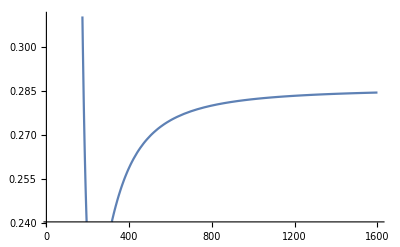

```mathematica
Plot[Subscript[R, g][λ]/. {d-> 20, α-> 1.8, β-> 1.6, γ-> 1.0, ζ-> 0}, {λ, 20, 1600}]
```

## Exact Solution

## Reflectance

```mathematica
Subscript[R, e][λ_] = Norm[r[λ]]// Simplify
```

Norm[((1+ⅇ^((4 ⅈ d π β)/λ)) α β+(-1+ⅇ^((4 ⅈ d π β)/λ)) β^2-(-1+ⅇ^((4 ⅈ d π β)/λ)) α (γ+ⅈ ζ+ξ)+(-1+ⅇ^((4 ⅈ d π β)/λ)) (ⅈ ζ+ξ) (γ+ⅈ ζ+ξ)-(1+ⅇ^((4 ⅈ d π β)/λ)) β (γ+2 ⅈ ζ+2 ξ))/((1+ⅇ^((4 ⅈ d π β)/λ)) α β-(-1+ⅇ^((4 ⅈ d π β)/λ)) β^2-(-1+ⅇ^((4 ⅈ d π β)/λ)) α (γ+ⅈ ζ+ξ)-ⅈ (-1+ⅇ^((4 ⅈ d π β)/λ)) (ζ-ⅈ ξ) (γ+ⅈ ζ+ξ)+(1+ⅇ^((4 ⅈ d π β)/λ)) β (γ+2 ⅈ ζ+2 ξ))]

## Plotting (constant ξ)

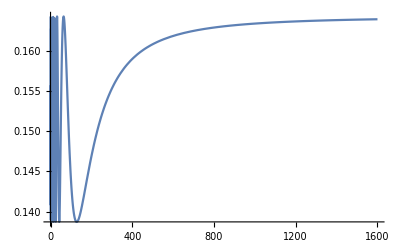

```mathematica
Plot[Subscript[R, e][λ] /. {d-> 20, α-> 1.8, β-> 1.6, γ-> 1.0, ξ-> 0.146, ζ-> 0}, {λ, 0, 1600}]
```

## Plotting (graphene ξ)

```mathematica
Subscript[R, ge][λ_] = Subscript[R, e][λ] /. ξ-> Subscript[ξ, g][λ];
```

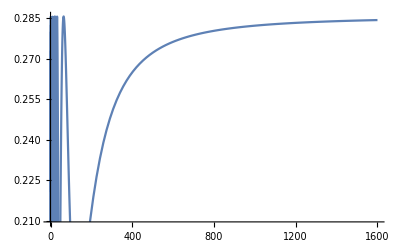

```mathematica
Plot[Subscript[R, ge][λ] /. {d-> 20, α-> 1.8, β-> 1.6, γ-> 1.0 , ζ-> 0}, {λ, 0, 1600}, PlotPoints->100]
```

## Analytical Approach

```mathematica
Subscript[R, 2][λ_] = Conjugate[r[λ]] r[λ] /. ζ-> 0 //FullSimplify// ComplexExpand // FullSimplify
```

(β^4+ξ^2 (γ+ξ)^2+β^2 (γ^2+6 γ ξ+6 ξ^2)+α^2 (β^2+(γ+ξ)^2)-2 α (ξ (γ+ξ)^2+β^2 (2 γ+3 ξ))-(α+β-ξ) (β-γ-ξ) (-α+β+ξ) (β+γ+ξ) Cos[(4 d π β)/λ])/(β^4+ξ^2 (γ+ξ)^2+β^2 (γ^2+6 γ ξ+6 ξ^2)+α^2 (β^2+(γ+ξ)^2)+2 α (ξ (γ+ξ)^2+β^2 (2 γ+3 ξ))+(β-γ-ξ) (α-β+ξ) (α+β+ξ) (β+γ+ξ) Cos[(4 d π β)/λ])

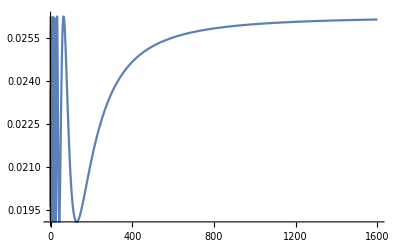

```mathematica
Plot[Subscript[R, 2][λ]/. {d-> 20, α-> 1.8, β-> 1.6, γ-> 1.0 , ξ-> 0.149}, {λ, 0, 1600}]
```